```mathematica
ClearAll["Global`*"]
(*Last Update: 17/06/2020*)
(*AndreHAM*)
```

# Brownian motion - Langevin equation

The Langevin equation could be used to describe the motian of a brownian particle due to its stochastic nature. The equation is derived directly from the Newton`s second Law  (F=m a=m(dv(t))/dt), considering  the existence of the fluid’s drag force and a random force due to the ambient molecules collisions:

	 											m(dv(t))/dt=-γv(t)+η(t),				v(t)=(dx(t))/dt
	 	
- m: particle mass;
- γ: friction term;
- v(t): particle velocity;
- x(t): particle position;
- η(t): Noise/Stochastic force

The noise term should satisfy some properties: 

i. <η(t)> =0
ii. <η_i(t)η_j(t')> =2 K_B T γδ_ij δ(t-t')

with temperature T, and Boltzmann cte K_B.

Approach:

To simulate the brownian motion we will discretize the langevin equation by finite difference in the following way:

v(t)=(dx(t))/dt→ v_i=(x_i-x_(i-1))/δt							m(v_i-v_(i-1))/δt=-γv_i+η_i

where δt is the time step. Notice, however, that the equality is only true for  δt→ 0.	v_i=(δt/m η_i+v_(i-1))/(1+δt/m γ)

Reference:

For a very interesting - more complete, complex - and useful paper on it I strongly recommend [1].

[1] Simulation of a Brownian particle in an optical trap, Volpe, G., Volpe, G.

## 1-D Simulation -

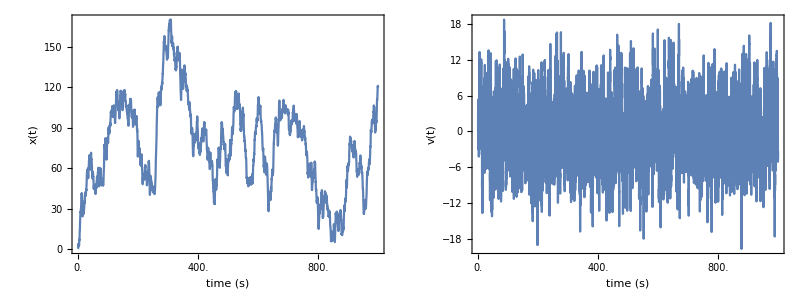

```mathematica
ClearAll["Global`*"]

δt=0.1; (* Discrete time difference *)
Tf=1000; (* final time - seconds *)
m=1; (* Particle mass *)
γ=2; (* Friction *)
kb=1; (* Boltzmann cte = 1 for simplicity *)
T=300; (* [k] - Temperature *)


(* Random noise *)
η=√(2 kb T γ)Table[RandomVariate[NormalDistribution[0,1]],{t,0,Tf/δt}];  (* 0 mean, 1 standard deviation *)

(* creating position and velocity tables (lists) *)
v=Table[0,{t,1,Tf/δt}];
x=Table[0,{t,1,Tf/δt}];

v[[1]]=0; (* Initial velocity *)
x[[1]]=0; (* Initial x-position *)




(* discrete time evolution *)
Do[v[[i]]=(δt/m η[[i]]+v[[i-1]])/(1+δt/m γ);
x[[i]]=x[[i-1]]+v[[i]]δt,{i,2,Tf/δt}]


(* Plot *)
Grid[{{
ListLinePlot[x,Frame->True,FrameTicks->{Automatic,{{#,δt #}&/@FindDivisions[{0.,Tf*10},5]//N,Automatic}},FrameLabel->{"time (s)","x(t)"},ImageSize->Large],
ListLinePlot[v,FrameTicks->{Automatic,{{#,δt #}&/@FindDivisions[{0.,Tf*10},5]//N,Automatic}},FrameLabel->{"time (s)","v(t)"},ImageSize->Large]
}}]
```

## 3-D Simulation -

```mathematica
ClearAll["Global`*"]


δt=0.1; (* Discrete time difference *)
Tf=10000; (* final time - seconds *)
m=1; (* Particle mass *)
γ=2; (* Friction *)
kb=1; (* Boltzmann cte = 1 for simplicity *)
T=300; (* [k] - Temperature *)


(* Random noise *)
η=√(2 kb T γ)Table[{RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1]]},{t,0,Tf/δt}];  (* 0 mean, 1 standard deviation *)

(* creating position and velocity tables (lists) *)
q=Table[{0,0,0},{t,1,Tf/δt}];
v=Table[{0,0,0},{t,1,Tf/δt}];

v[[1]]={0,0,0}; (* Initial velocity *)
q[[1]]={0,0,0}; (* Initial x-position *)



(* discrete time evolution *)
Do[v[[i,j]]=(δt/m η[[i,j]]+v[[i-1,j]])/(1+δt/m γ);
q[[i,j]]=q[[i-1,j]]+v[[i,j]]δt,

{i,2,Tf/δt},{j,1,3}]


(* 3D Plot *)
Grid[{{
ListPointPlot3D[v,ImageSize->Large,PlotLabel->"Velocity - v[t] = (vx[t],vy[t],vz[t])",AxesLabel->{"vx","vy","vz"}],
ListPointPlot3D[q,ImageSize->Large,PlotLabel->"Position - q[t] = (x[t],y[t],z[t])",AxesLabel->{"x","y","z"}]
}}]
```

-Graphics3D- | -Graphics3D-